```mathematica
Needs["ErrorBarPlots`"]
```

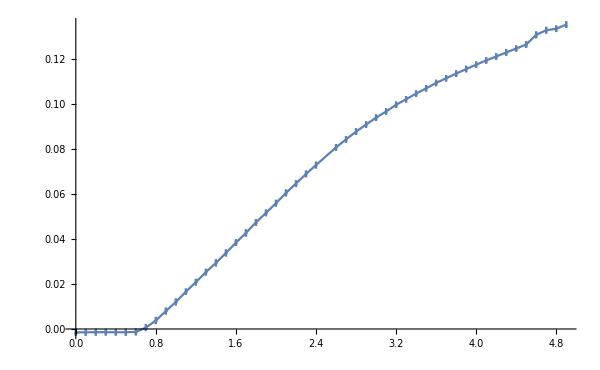
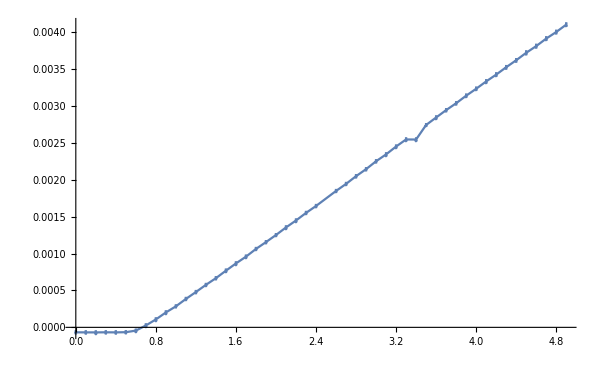
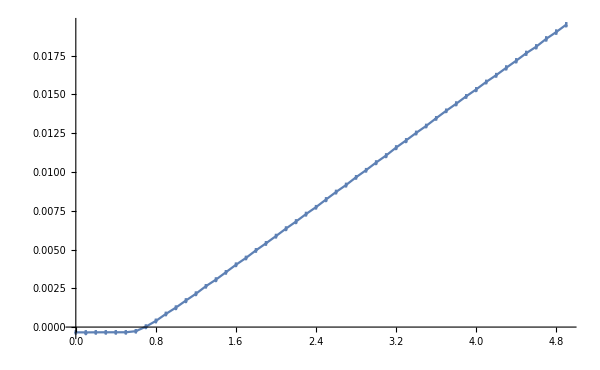
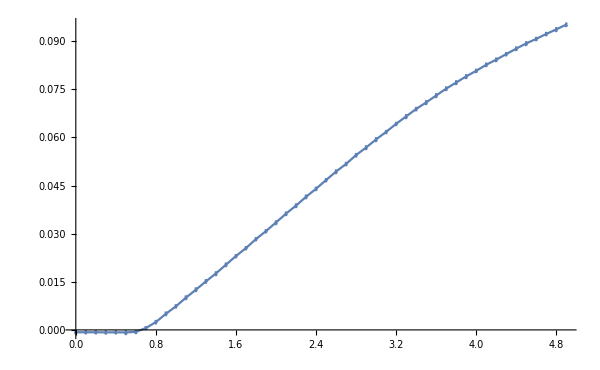
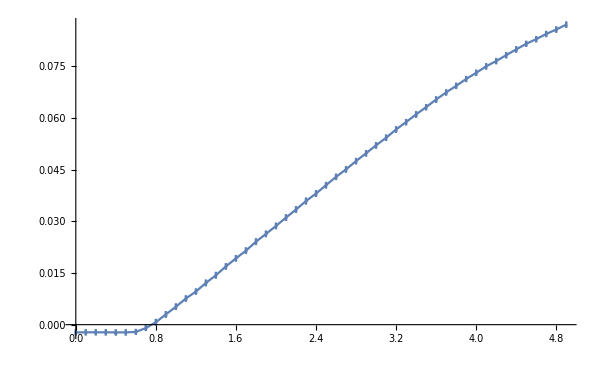
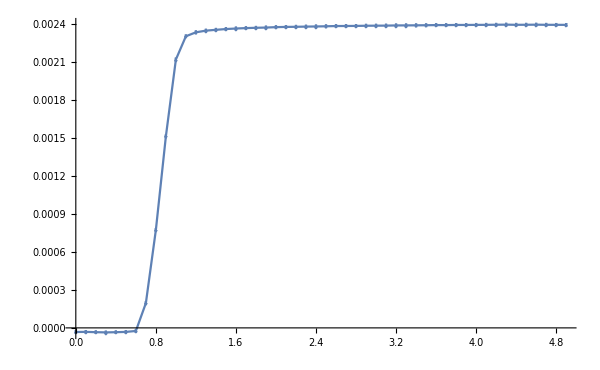
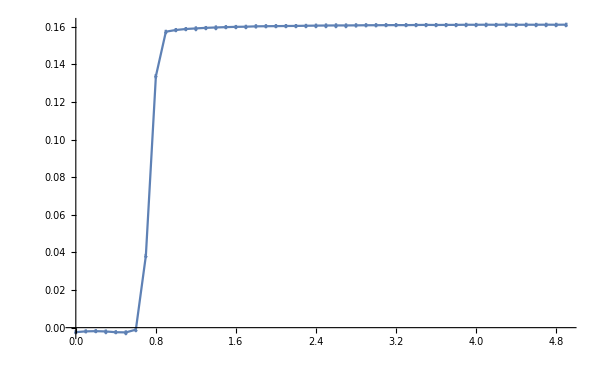
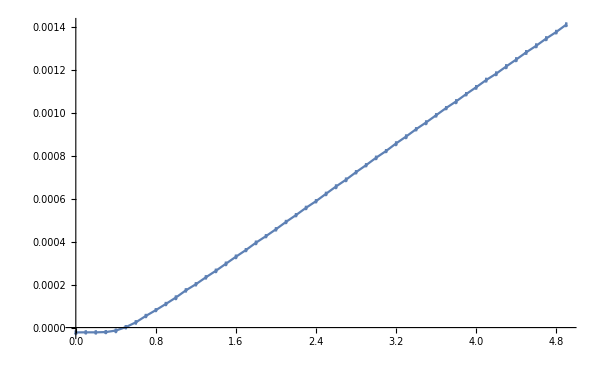

```mathematica
plot[type_] := Module[{data},
data = Import["~/phys3112/lab4/"<>type[[1]]<>".tsv"][[4;;-2]];
data = {{#[[1]], #[[2]]/type[[2]]}, ErrorBar[#[[3]]/type[[2]]]}&/@data;
ErrorListPlot[data, PlotMarkers->{"◆", 5}, PlotRange->All, Joined->True, ImageSize->600]
]
plot /@ {{"2N3904-10Ohm", 10},
{"2N3904-1kOhm", 1000},
{"2N3904-200Ohm", 200},
{"2N3904-25Ohm", 25},
{"2N3904-30Ohm", 30},
{"2N3904-Alt-2kOhm", 2000},
{"2N3904-Alt-30Ohm", 30},
{"Diode-3kOhm", 3000}}
```